```mathematica
Quit[];
```

```mathematica
<<FeynCalc`
```

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

See also the supplied examples. If you use FeynCalc in your research, please cite

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

FeynCalc 9.3.0 (development version). For help, use the documentation center, check out the wiki or write to the mailing list.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

See also the supplied examples. If you use FeynCalc in your research, please cite

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

FeynCalc 9.3.0 (development version). For help, use the documentation center, check out the wiki or write to the mailing list.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

See also the supplied examples. If you use FeynCalc in your research, please cite

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

FeynCalc 9.3.0 (development version). For help, use the documentation center, check out the wiki or write to the mailing list.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

See also the supplied examples. If you use FeynCalc in your research, please cite

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

FeynCalc 9.3.0 (development version). For help, use the documentation center, check out the wiki or write to the mailing list.

```mathematica
αem = 1/137;
```

```mathematica
me=5.11*10^-4;
```

```mathematica
Q2max[x_, Ee_]= 4.0;
Q2min[x_] = me^2 x^2/(1-x);
```

```mathematica
f1[x_,see_] = αem/π(((1 - x + x^2/2)/x)Log[Q2max[x,Ee]/Q2min[x]] - me^2 x/Q2min[x](1 - Q2min[x]/Q2max[x,Ee]))/.Ee-> Sqrt[see]/2;
```

```mathematica
f[w_,see_]:= 2/Sqrt[see] f1[2 w/Sqrt[see],see];
```

```mathematica
f2[x_?NumericQ,see_?NumericQ] := αem/(π*x)(-1 + (x + (((5.11*10^-4)^2)/see - 1)x^2)/(1 - x) + (2 - 2x + x^2)Log[Sqrt[see](1 -x)/(5.11*10^-4*x)]);
```

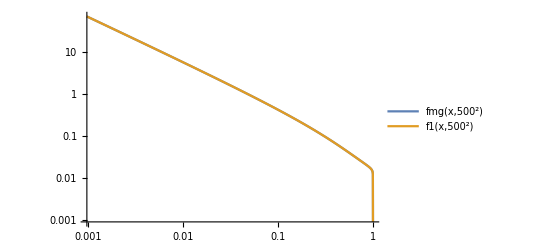

```mathematica
LogLogPlot[{fmg[x,500^2],f1[x,500^2]},{x,0,1}, PlotLegends->"Expressions"]
```

```mathematica
FCClearScalarProducts[]
```

```mathematica
Ms =(SP[k1,k2] Subscript[c, w]^2 g*MT[μ,ν] - Subscript[c, w]^2 g*FV[k1,ν]FV[k2,μ])(SP[p1,p2] Subscript[c, w]^2 g*MT[α,β] - Subscript[c, w]^2 g*FV[p1,β]FV[p2,α])1/(SP[k1+k2,k1+k2] - Subscript[m, a]^2+ ⅈ*Subscript[m, a]*Subscript[Γ, a])PolarizationVector[k1,μ,Transversality->True]PolarizationVector[k2,ν,Transversality->True]PolarizationVector[p1,α,Transversality->True]PolarizationVector[p2,β,Transversality->True];
Mt = (SP[k1,-p1] Subscript[c, w]^2 g*MT[μ,α] - Subscript[c, w]^2 g*FV[k1,α]FV[-p1,μ])(SP[k2,-p2] Subscript[c, w]^2 g*MT[ν,β] - Subscript[c, w]^2 g*FV[k2,β]FV[-p2,ν])1/(SP[k1-p1,k1-p1] - Subscript[m, a]^2+ ⅈ*Subscript[m, a]*Subscript[Γ, a])PolarizationVector[k1,μ,Transversality->True]PolarizationVector[k2,ν,Transversality->True]PolarizationVector[p1,α,Transversality->True]PolarizationVector[p2,β,Transversality->True];
Mu = (SP[k1,-p2] Subscript[c, w]^2 g*MT[μ,β] - Subscript[c, w]^2 g*FV[k1,β]FV[-p2,μ])(SP[k2,-p1] Subscript[c, w]^2 g*MT[α,ν] - Subscript[c, w]^2 g*FV[k2,α]FV[-p1,ν])1/(SP[k1-p2,k1-p2] - Subscript[m, a]^2+ ⅈ*Subscript[m, a]*Subscript[Γ, a])PolarizationVector[k1,μ,Transversality->True]PolarizationVector[k2,ν,Transversality->True]PolarizationVector[p1,α,Transversality->True]PolarizationVector[p2,β,Transversality->True];
```

```mathematica
Subscript[Γ, a] = (g^2*Subscript[c, w]^4*Subscript[m, a]^3)/(64*π);
```

```mathematica
M1 = (Ms + Mt + Mu);
```

```mathematica
M1
```

((ε̄)^μ(k1) (ε̄)^ν(k2) (ε̄)^α(p1) (ε̄)^β(p2) (g c_w^2 (ḡ)^μν (OverBar[k1]·OverBar[k2])-g c_w^2 OverBar[k1]^ν OverBar[k2]^μ) (g c_w^2 (ḡ)^αβ (OverBar[p1]·OverBar[p2])-g c_w^2 OverBar[p1]^β OverBar[p2]^α))/((OverBar[k1]+OverBar[k2])^2+(ⅈ g^2 m_a^4 c_w^4)/(64 π)-m_a^2)

```mathematica
M2 = M1//Contract//Simplify;
```

```mathematica
M2
```

(64 π g^2 c_w^4 ((OverBar[k1]·ε̄(k2)) (OverBar[k2]·ε̄(k1))-1/2 S (ε̄(k1)·ε̄(k2))) ((OverBar[p1]·ε̄(p2)) (OverBar[p2]·ε̄(p1))-1/2 S (ε̄(p1)·ε̄(p2))))/(ⅈ g^2 m_a^4 c_w^4-64 π m_a^2+64 π S)

```mathematica
M2
```

(64 π g^2 c_w^4 ((OverBar[k1]·ε̄(k2)) (OverBar[k2]·ε̄(k1))-1/2 S (ε̄(k1)·ε̄(k2))) ((OverBar[p1]·ε̄(p2)) (OverBar[p2]·ε̄(p1))-1/2 S (ε̄(p1)·ε̄(p2))))/(ⅈ g^2 m_a^4 c_w^4-64 π m_a^2+64 π S)

```mathematica
SP[k1,k1] = 0;
SP[k2,k2] = 0;
SP[p1,p1] = 0;
SP[p2,p2] = 0;
SP[k1,k2] = 2 En^2/.En->Sqrt[S]/2;
SP[k1,p1] = En^2(1 - Cos[θ])/.En->Sqrt[S]/2;
SP[k1,p2] = En^2(1 + Cos[θ])/.En->Sqrt[S]/2;
SP[k2,p1] = En^2(1 + Cos[θ])/.En->Sqrt[S]/2;
SP[k2,p2] = En^2(1 - Cos[θ])/.En->Sqrt[S]/2;
SP[p1,p2] = 2 En^2/.En->Sqrt[S]/2;
```

```mathematica
ampSquared[0] = Simplify[
(DoPolarizationSums[#1, k1,0]&) [
(DoPolarizationSums[#1, k2,0]&) [
(DoPolarizationSums[#1, p1,0]&) [
(DoPolarizationSums[#1, p2,0]&) [
FeynAmpDenominatorExplicit[M2*ComplexConjugate[M2]]
]
]
]
]
];
```

```mathematica
M3 = ComplexExpand[ampSquared[0]]//Simplify;
```

```mathematica
M3/.g-> 10^-3/.Subscript[c, w]-> 0.88153/.Subscript[m, a]-> 20/.S-> 20^2/.θ-> 0
```

40425.7

```mathematica
dσdpt[s_,mass_,pt_,ga_] := 1/(2.56819*10^-9)*1/(32π*s)*((4*pt)/(s*Sqrt[1 - 4 pt^2/s]))M3/.S->s/.pT-> pt/.Subscript[m, a]-> mass/.g-> ga/.Subscript[c, w]->0.88153;
```

```mathematica
dσdpt[50^2,51,24,10^-3]
```

0.296702

```mathematica
dσdsdpt[s_,se_,ptmin_,η_, mass_,g_]:=  Integrate[1/s*1/x f2[x,se]f2[s/(se*x),se]dσdpt[s,mass,pt,g],{pt,ptmin,Sqrt[s/2]},{x,(s*Exp[-η])/(2*Sqrt[se]pt)(1 + Sqrt[1 - 4*pt^2/s]),(s*Exp[η])/(2*Sqrt[se]pt)(1 - Sqrt[1 - 4*pt^2/s])}];
```

```mathematica
Subscript[s, ee] = 500^2;Subscript[m, a] = 30;Subscript[g, aBB] = 10^-3; Subscript[pt, cut] = 0; Subscript[η, cut] = 2.5;
```

```mathematica
LogPlot[{dσdsdpt[sqrts^2,Subscript[s, ee],Subscript[pt, cut],Subscript[η, cut],Subscript[m, a],Subscript[g, aBB]]},{sqrts,5,10},PlotRange->Full]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 21 recursive bisections in pt near {pt,x} = {0.707107,0.105515}. NIntegrate obtained 1165.89-2054.68 ⅈ and 11.7186 for the integral and error estimates.

$Aborted

```mathematica
M4[s_,α_]:= M3/.S-> s/.θ-> α
```

```mathematica
(*BELOW HERE IS PARTONIC LEVEL CROSS SECTION*)
```

```mathematica
σ10[s_] := NIntegrate[1/(2.56819*10^-9)1/(32π s)Sin[α]M4[s,α]/.Subscript[m, a]-> 10/.g-> 10^-3/.Subscript[c, w]->0.88153 ,{α,10*π/180,π/2}];
σ25[s_] := NIntegrate[1/(2.56819*10^-9)1/(32π s)Sin[α]M4[s,α]/.Subscript[m, a]-> 25/.g-> 10^-3/.Subscript[c, w]->0.88153 ,{α,10*π/180,π/2}];
σ50[s_] := NIntegrate[1/(2.56819*10^-9)1/(32π s)Sin[α]M4[s,α]/.Subscript[m, a]-> 50/.g-> 10^-3/.Subscript[c, w]->0.88153 ,{α,10*π/180 0,π/2}];
σ100[s_] := NIntegrate[1/(2.56819*10^-9)1/(32π s)Sin[α]M4[s,α]/.Subscript[m, a]-> 100/.g-> 10^-3/.Subscript[c, w]->0.88153 ,{α,10*π/180,π/2}];
σ200[s_] := NIntegrate[1/(2.56819*10^-9)1/(32π s)Sin[α]M4[s,α]/.Subscript[m, a]-> 200/.g-> 10^-3/.Subscript[c, w]->0.88153 ,{α,10*π/180,π/2}];
```

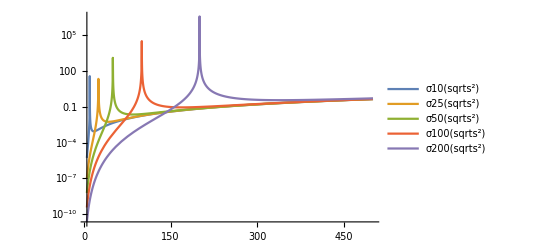

```mathematica
LogPlot[{σ10[sqrts^2],σ25[sqrts^2],σ50[sqrts^2],σ100[sqrts^2], σ200[sqrts^2]},{sqrts,5,500}, PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
(*Here are the helicity amplitudes for the hard scattering γγ -> a -> γγ)
```

```mathematica
Subscript[M, pmpm][u_]= -Subscript[g, sbb]4*u^2/(u^2 - Subscript[m, a]^2);
Subscript[M, pmmp][t_]=  -Subscript[g, sbb]4*t^2/(t^2 - Subscript[m, a]^2);
Subscript[M, ppmm] [s_,t_,u_]= 4 Subscript[g, sbb]*(s^2(s - Subscript[m, a]^2)/((s-Subscript[m, a]^2)^2 + Subscript[m, a]^2 Subscript[Γ, a]^2) + (t^2/(t - Subscript[m, a]^2)) + u^2/(u - Subscript[m, a]^2)) -ⅈ Subscript[g, sbb] 4((s^2 Subscript[m, a] Subscript[Γ, a])/((s - Subscript[m, a]^2)^2 + Subscript[m, a]^2 Subscript[Γ, a]^2));
Subscript[M, pppp][s_] = -Subscript[g, sbb]4(s^2(s - Subscript[m, a]^2)/((s-Subscript[m, a]^2)^2 + Subscript[m, a]^2 Subscript[Γ, a]^2)) + ⅈ Subscript[g, sbb] 4(s^2 Subscript[m, a] Subscript[Γ, a])/((s - Subscript[m, a]^2)^2 + Subscript[m, a]^2 Subscript[Γ, a]^2);
```

```mathematica
Subscript[M, pp][s_,t_,u_] = Subscript[M, ppmm][s,t,u] + Subscript[M, pppp][s];
Subscript[M, pm][s_,t_,u_] = Subscript[M, pmmp][t] + Subscript[M, pmpm][u];
Subscript[M, mm][s_,t_,u_] = Subscript[M, ppmm][s,t,u] + Subscript[M, pppp][s];
```

```mathematica
Subscript[σ, pp][m_] := NIntegrate[1/(2.56819*10^-9)1/(32π s)(Subscript[M, pp][s,-s/2(1 - Cos[θ]),-s/2(1 + Cos[θ])])^2/.s-> 150/.Subscript[m, a]-> m/.Subscript[g, sbb]-> 10^-4/.Subscript[c, w]->0.88153 ,{θ,0.0,π}];
Subscript[sσ, pm][m_] := NIntegrate[1/(2.56819*10^-9)1/(32π s)(Subscript[M, pm][s,-s/2(1 - Cos[θ]),-s/2(1 + Cos[θ])])^2/.s-> 150/.Subscript[m, a]-> m/.Subscript[g, sbb]-> 10^-4/.Subscript[c, w]->0.88153 ,{θ,0.0,π}];
Subscript[σ, pm][m_] := NIntegrate[1/(2.56819*10^-9)1/(32π s)(Subscript[M, pm][s,-s/2(1 - Cos[θ]),-s/2(1 + Cos[θ])])^2/.s-> 150/.Subscript[m, a]-> m/.Subscript[g, sbb]-> 10^-4/.Subscript[c, w]->0.88153 ,{θ,0.0,π}];
Subscript[σ, mm][m_] := NIntegrate[1/(2.56819*10^-9)1/(32π s)(Subscript[M, mm][s,-s/2(1 - Cos[θ]),-s/2(1 + Cos[θ])])^2/.s-> 150/.Subscript[m, a]-> m/.Subscript[g, sbb]-> 10^-4/.Subscript[c, w]->0.88153 ,{θ,0.0,π}];
```

```mathematica
LogPlot[{Subscript[σ, pp][m],Subscript[σ, pm][m]}, {m, 100, 500},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
t = PlusMinus[-s/2 ,s/2 Y]
```

-s/2±(s Y)/2

```mathematica
dt = MinusPlus[2 pt/Y]
```

∓(2 pt)/Y

```mathematica
FullSimplify[((s + t)/t + t/(t + s))dt,Assumptions->{pt∈Reals,s∈Reals}]
```

∓(2 pt)/Y (s^2/((-s/2±(s Y)/2)^2+s (-s/2±(s Y)/2))+2)

```mathematica
t*(s+t)//Expand
```

(-s/2±(s Y)/2)^2+s (-s/2±(s Y)/2)

```mathematica
t-> PlusMinus[-s/2,s/2 Sqrt[1 - 4 pt^2/s]]
```

t→-s/2±1/2 s √(1-(4 pt^2)/s)

```mathematica
cos(θ) = 1 + 2t/s
```

```mathematica
D[t,pt]
```

0

```mathematica
t= -s/2 + s/2 Sqrt[1 - 4 pt^2/s]
```

1/2 s √(1-(4 pt^2)/s)-s/2

```mathematica
D[t,pt]
```

0

```mathematica
D[t,pt]
```

-(2 pt)/(√(1-(4 pt^2)/s))

```mathematica
αem = 1/137;
Subscript[m, e] = 5.11*10^-4;
```

```mathematica
q2min[x_]:= Subscript[m, e]^2 x^2/(1 - x);
```

```mathematica
f[x_] := αem/(2π)((1 + (1-x)^2)Log[2/q2min[x]] - 2 Subscript[m, e]^2 x^2(1/q2min[x] - 1/2))
```

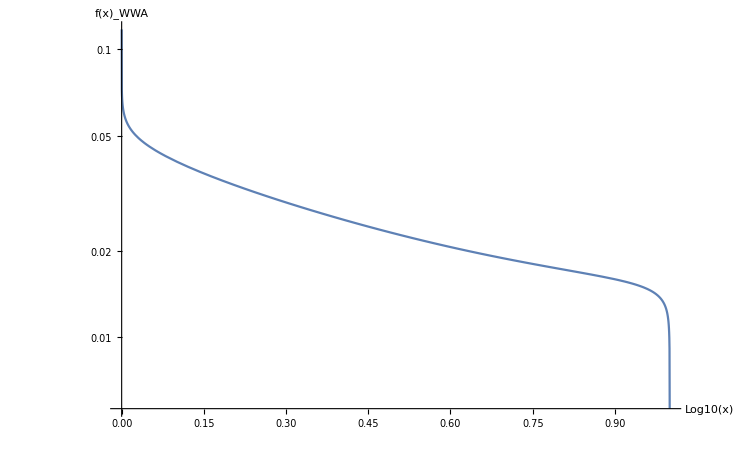

```mathematica
LogPlot[f[x],{x,0,1},AxesLabel->{Style["Log10(x)", Black,FontSize-> 25],Style["f(x)_WWA", Black,FontSize-> 25]}, TicksStyle->Directive[Black, 20]]
```